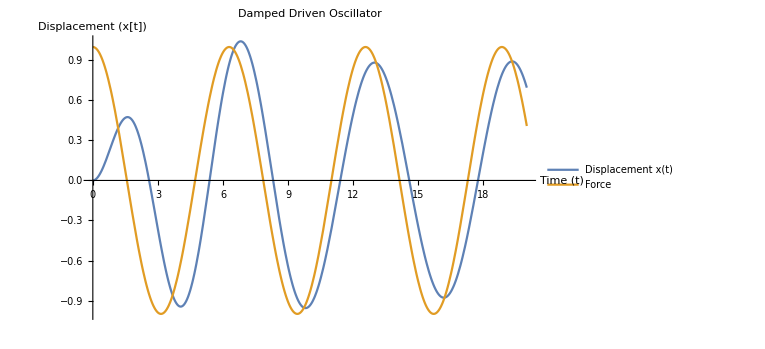

```mathematica
m=1; (*Mass*)
c=0.5; (*Damping coefficient*)
k=2; (*Spring constant*)
F0=1; (*Amplitude of the driving force*)
ω=1; (*Driving frequency*)

eqn=m x''[t]+c x'[t]+k x[t]==F0 Cos[ω t];
sol=NDSolve[{eqn,x[0]==0,x'[0]==0},x,{t,0,50}];
Plot[{Evaluate[x[t]/. sol],F0 Cos[ω t]},{t,0,20},PlotLabel->"Damped Driven Oscillator",PlotLegends->{"Displacement x(t)","Force"}, AxesLabel->{"Time (t)","Displacement (x[t])"}]
```

{0.3,0.05}

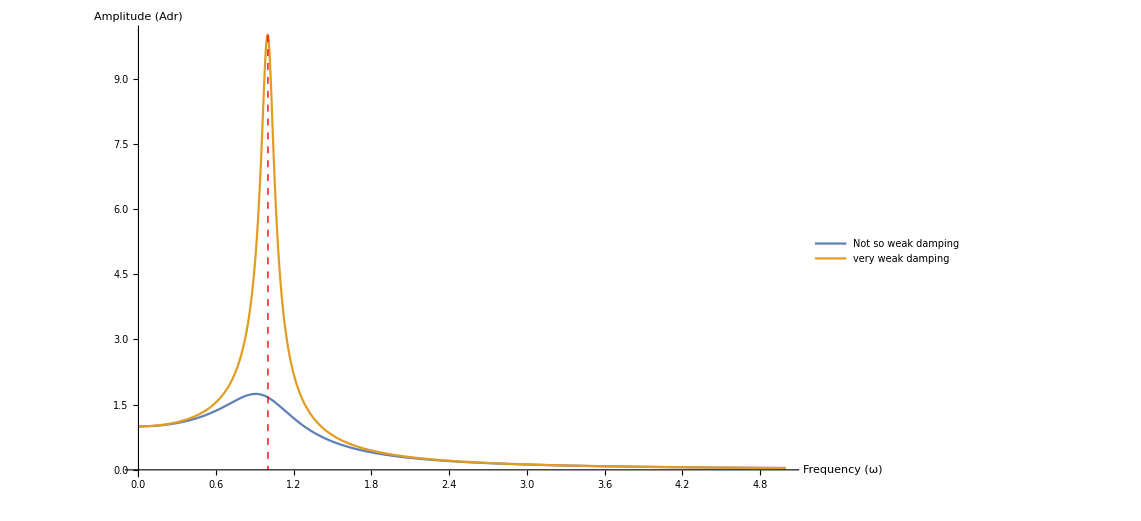

```mathematica
(* Resonance *)
m=1; (*Mass*)
b={0.3,0.05}; (*Damping coefficients*)
k=1; (*Spring constant*)
F0=1; (*Amplitude of the driving force*)
(*ω=1; (*Driving frequency*)*)
ω0=√(k/m)(*Natural frequency*);
b/ω0
Adr=(F0/m)/(√((ω0^2-x^2)^2+4 b^2 x^2));
(*Define the x-coordinate where you want to draw the vertical line*)
xLine=1;
Plot[Adr,{x,0,5}, PlotRange->All,PlotLegends->{"Not so weak damping","very weak damping"},AxesLabel->{"Frequency (ω)","Amplitude (Adr)"},Epilog->{Red,Dashed,Line[{{xLine,10},{xLine,0}}]}]
```